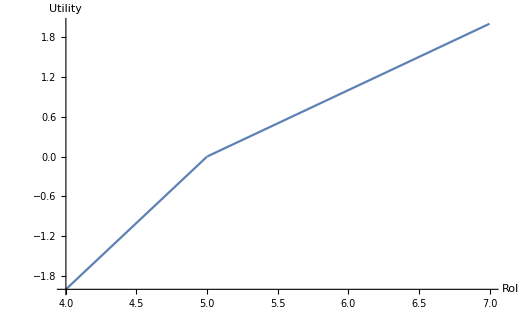

```mathematica
Plot[Max[x-5,0]-2Max[5-x,0],{x,4,7},AxesLabel->{"RoI","Utility"},AxesOrigin->{4,-2},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14}]
```

```mathematica
stocks={"MSFT"};
y=2015;
```

```mathematica
solveObjective[{"MSFT"},2015];
```

LinearProgramming::lpsub: This problem is unbounded.

```mathematica
xs=Flatten[x[y]/@stocks,1]
```

{{5,1,46.43,0.237129,0.197544,27913900},{1,2,46.,0.2301,0.196009,39673900},{2,2,45.33,0.230426,0.195036,36447900},{3,2,45.9,0.230108,0.19015,29114100},{4,2,47.25,0.236337,0.191929,29645200},{5,2,46.86,0.255228,0.200878,23942800},{1,3,46.27,0.256496,0.201811,23651900},{2,3,46.03,0.260165,0.201952,35270600},{3,3,45.64,0.259932,0.197438,29719600},{4,3,45.16,0.230701,0.196825,32742300},{5,3,45.91,0.229525,0.197978,35695300},{2,4,46.06,0.189,0.201269,36161900},{3,4,45.6,0.1891,0.19714,39081100},{4,4,46.8,0.188835,0.19823,35898000},{5,4,46.85,0.2112,0.20719,26211600},{1,5,46.68,0.210478,0.207225,42525500},{2,5,42.36,0.21005,0.207321,169164000},{3,5,40.9,0.408553,0.298085,84507100},{4,5,41.71,0.422401,0.306784,63585300},{5,5,40.11,0.432629,0.311285,78004900},{1,6,40.99,0.446797,0.321611,50352500},{2,6,41.31,0.459333,0.326327,52082400},{3,6,41.54,0.46072,0.3259,41614800},{4,6,42.15,0.457737,0.325331,36548200},{5,6,42.11,0.44549,0.327436,34311700},{1,7,42.06,0.445767,0.327451,31381100},{2,7,42.3,0.445187,0.32691,29670700},{3,7,42.08,0.446889,0.327327,38262500},{4,7,42.79,0.446631,0.32432,33268800},{5,7,43.56,0.452274,0.327327,40264900},{2,8,43.58,0.453116,0.330242,33695700},{3,8,43.53,0.452709,0.327817,27111700},{4,8,43.5,0.451907,0.327497,27603400},{5,8,43.86,0.43867,0.326108,29721100},{1,9,44.15,0.440569,0.326887,32518800},{2,9,44.09,0.442087,0.325989,25271700},{3,9,43.99,0.254059,0.325601,29759800},{4,9,44.06,0.211346,0.325511,28957300},{5,9,43.85,0.202517,0.325375,33807700},{1,10,43.88,0.127555,0.317054,31924000},{2,10,43.28,0.110085,0.31557,31748600},{3,10,43.06,0.125487,0.303845,25748700},{4,10,43.11,0.127775,0.303737,23193500},{5,10,42.36,0.118102,0.303164,36248800},{1,11,42.85,0.136366,0.303897,32108000},{2,11,42.03,0.142121,0.305424,39159700},{3,11,41.98,0.158735,0.307802,32215300},{4,11,41.02,0.157677,0.307438,59992500},{5,11,41.38,0.164694,0.310701,58007700},{1,12,41.56,0.152028,0.310933,35273500},{2,12,41.7,0.153805,0.310624,31673400},{3,12,42.5,0.15523,0.310444,44194800},{4,12,42.29,0.17351,0.312615,33679100},{5,12,42.88,0.170052,0.311068,71509000},{1,13,42.86,0.177055,0.305073,26049000},{2,13,42.9,0.177098,0.30474,25389500},{3,13,41.46,0.177284,0.303757,43136500},{4,13,41.21,0.213195,0.31255,37466500},{5,13,40.97,0.213377,0.312336,33820300},{1,14,40.96,0.213008,0.311845,34697100},{2,14,40.66,0.209648,0.308941,34802600},{3,14,40.72,0.210139,0.30887,36752000},{4,14,40.29,0.210229,0.308507,37451600},{1,15,41.55,0.204962,0.301985,39083900},{2,15,41.53,0.233632,0.311492,28758500},{3,15,41.42,0.223504,0.311511,24603400},{4,15,41.48,0.223619,0.221304,25664100}}

```mathematica
Standardize[{0,1}]
```

{-1/(√2),1/(√2)}

```mathematica
newXs=Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,xs]//N;
```

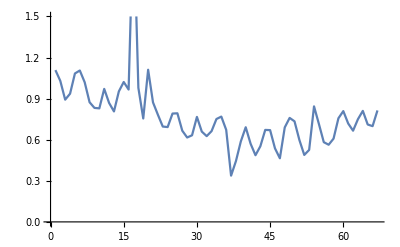

```mathematica
ListLinePlot[Norm/@newXs]
```

```mathematica
g=2f;
g[x]
```

(2 f)[x]

```mathematica
Hold
```

```mathematica
FullForm[f[##]&]
```

Function[f[SlotSequence[1]]]

```mathematica
Function[##^2]
```

##1^2&

```mathematica
D=.
```

Unset::wrsym: Symbol D is Protected.

$Failed

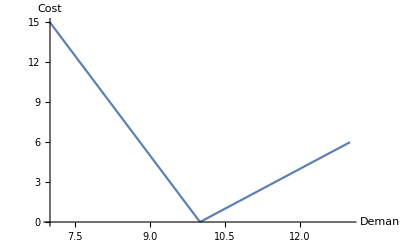

```mathematica
Plot[5Max[10-x,0]+2Max[x-10,0],{x,7,13},AxesLabel->{"Demand","Cost"},BaseStyle->{FontFamily->"Helvetica",FontSize->14}]
```

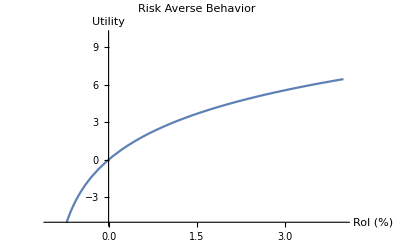

```mathematica
Plot[{4Log[x+1]},{x,-2,4},AxesLabel->{"RoI (%)","Utility"},PlotRange->{-5,10},AxesOrigin->{0,-5},Axes->{True,True},BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotLabel->"Risk Averse Behavior"]
```

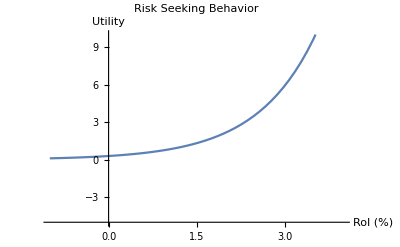

```mathematica
Plot[{.8Exp[x-1]},{x,-1,4},AxesLabel->{"RoI (%)","Utility"},PlotRange->{-5,10},AxesOrigin->{0,-5},Axes->{True,True},BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotLabel->"Risk Seeking Behavior"]
```